```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[]

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[2],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];



rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

/Users/Michael/Desktop/famod/mathematica

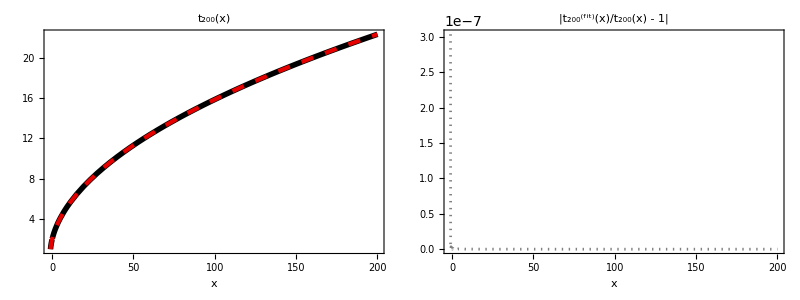

(63.21975933390082 + 380.08563149296145*x + 810.2307212043552*Power(x,2) + 585.0129686787305*Power(x,3) - 406.6714931011936*Power(x,4) - 1003.2879972442737*Power(x,5) - 
     633.4140610182495*Power(x,6) - 63.549331542631045*Power(x,7) + 114.54636074466283*Power(x,8) + 62.011233002217395*Power(x,9) + 13.750682148451842*Power(x,10) + 
     1.4604810282159304*Power(x,11) + 0.07252235160524895*Power(x,12) + 0.001567857330443711*Power(x,13) + 0.000013272370337623199*Power(x,14) + 
     3.660522335594211e-8*Power(x,15) + 2.1251579740535422e-11*Power(x,16))/
   (31.609879640022022 + 179.5061893290641*x + 347.38729112508554*Power(x,2) + 187.77466277293303*Power(x,3) - 247.39515928702926*Power(x,4) - 
     414.05598505483044*Power(x,5) - 196.62441712412095*Power(x,6) + 13.796301325027898*Power(x,7) + 47.20534483149715*Power(x,8) + 17.872426954407864*Power(x,9) + 
     2.9248857075582086*Power(x,10) + 0.22164902064018988*Power(x,11) + 0.007474229419816371*Power(x,12) + 0.00010364823859082527*Power(x,13) + 
     5.187322323753321e-7*Power(x,14) + 7.174936385850154e-10*Power(x,15) + 1.175247329467607e-13*Power(x,16))

```mathematica
δ=0.001;

t200[x_] = Piecewise[{{1.+(1.+x)*ArcTan[Sqrt[x]]/Sqrt[x],x>δ},{2.+0.6666666666666667 x-0.1333333333333333 x^2+0.05714285714285716 x^3-0.031746031746031744 x^4+0.020202020202020193 x^5-0.013986013986013984 x^6+0.010256410256410262 x^7-0.00784313725490196 x^8+0.006191950464396287 x^9-0.005012531328320802 x^10,-δ≤x≤δ},{1.+(1.+x)*ArcTanh[Sqrt[-x]]/Sqrt[-x], -1.<x<-δ},{1.0,x==-1.0}}];

xmin = -0.999;
xmax = 200;
xstep=0.01;
tdata=Table[{x,t200[x]},{x,xmin,xmax,xstep}];

n = 16;

t200fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t200[x],t200fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_200(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t200fit[x]/t200[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_200^(fit)(x)/t_200(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t200fit[x]//CForm
```

```mathematica
Series[1.+(1.+x)*ArcTan[Sqrt[x]]/Sqrt[x],{x,0,10}];
```

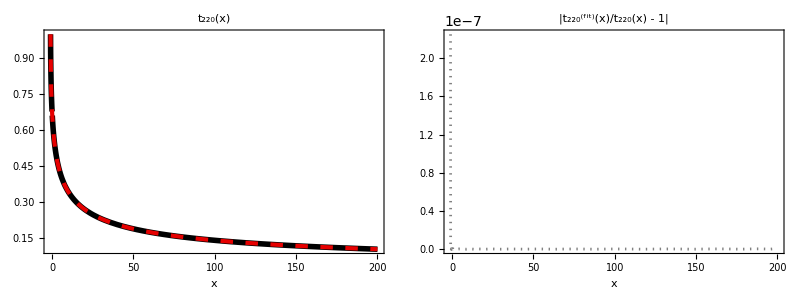

(456.0717685013072 + 6138.497799670426*x + 18415.553046770605*Power(x,2) + 19691.7172421894*Power(x,3) + 2898.2127968410837*Power(x,4) - 3614.6523331460667*Power(x,5) + 
     11389.611697391874*Power(x,6) + 21474.826796208286*Power(x,7) + 14871.90337130695*Power(x,8) + 5219.601958438456*Power(x,9) + 964.6137551732895*Power(x,10) + 
     89.7736374260045*Power(x,11) + 3.866194043736338*Power(x,12) + 0.06912592028121776*Power(x,13) + 0.00044196551466947056*Power(x,14) + 
     7.664395594410113e-7*Power(x,15) + 1.539335288358236e-10*Power(x,16))/
   (684.1076528076261 + 9344.568232901041*x + 29433.605444732875*Power(x,2) + 34655.91053674811*Power(x,3) + 9179.8694508414*Power(x,4) - 5423.728248733478*Power(x,5) + 
     16156.69594073634*Power(x,6) + 35777.20320424328*Power(x,7) + 27919.78865897606*Power(x,8) + 11204.510344427128*Power(x,9) + 2454.1159153285016*Power(x,10) + 
     285.7976201827534*Power(x,11) + 16.501831546099268*Power(x,12) + 0.42876486959188886*Power(x,13) + 0.0044186084191126206*Power(x,14) + 
     0.000014810477376582228*Power(x,15) + 1.0341668485008954e-8*Power(x,16))

```mathematica
δ=0.001;

t220[x_] = Piecewise[{{(-1.0+(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/x,x>δ},{0.6666666666666667-0.1333333333333333 x+0.05714285714285716 x^2-0.031746031746031744 x^3+0.020202020202020193 x^4-0.013986013986013984 x^5+0.010256410256410262 x^6-0.00784313725490196 x^7+0.006191950464396287 x^8-0.005012531328320802 x^9+0.0041407867494824 x^10,-δ≤x≤δ},{(-1.0+(x+1.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/x, -1.<x<-δ},{1.0,x==-1.0}}];

xmin = -0.999;
xmax = 200;
xstep=0.01;
tdata=Table[{x,t220[x]},{x,xmin,xmax,xstep}];

n = 16;

t220fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t220[x],t220fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_220(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t220fit[x]/t220[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_220^(fit)(x)/t_220(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t220fit[x]//CForm
```

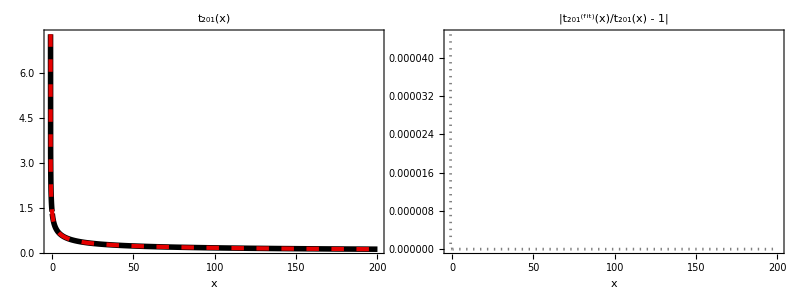

(-5727.780276245886 - 16656.917423117204*x - 12506.70489796712*Power(x,2) + 3533.6365352963835*Power(x,3) + 4046.8720268359707*Power(x,4) - 3633.102683844837*Power(x,5) + 
     396.3241468432578*Power(x,6) + 10198.392446287147*Power(x,7) + 14219.720976200637*Power(x,8) + 10469.868083059493*Power(x,9) + 4309.651396082802*Power(x,10) + 
     908.7020129548255*Power(x,11) + 85.53600401445127*Power(x,12) + 3.0784088039656656*Power(x,13) + 0.035776352295545606*Power(x,14) + 
     0.00010211822898423643*Power(x,15) + 3.095818533435384e-8*Power(x,16))/
   (-4295.835228827275 - 14211.022782730835*x - 13959.795028128196*Power(x,2) - 97.67311371562538*Power(x,3) + 4529.779558944654*Power(x,4) - 
     1934.3935160008843*Power(x,5) - 871.0058673904322*Power(x,6) + 8044.423723562404*Power(x,7) + 13564.43982013535*Power(x,8) + 11468.467869290651*Power(x,9) + 
     5647.292037835587*Power(x,10) + 1541.8604492584877*Power(x,11) + 208.53309737071402*Power(x,12) + 11.992399966996727*Power(x,13) + 0.24786621578918133*Power(x,14) + 
     0.0014919746956868216*Power(x,15) + 1.689074902336641e-6*Power(x,16))

```mathematica
δ=0.001;

t201[x_] = Piecewise[{{(1.0+(x-1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/x,x>δ},{1.3333333333333333-0.5333333333333333 x+0.34285714285714286 x^2-0.25396825396825395 x^3+0.20202020202020202 x^4-0.16783216783216784 x^5+0.14358974358974358 x^6-0.12549019607843137 x^7+0.11145510835913312 x^8-0.10025062656641603 x^9+0.09109730848861283 x^10,-δ≤x≤δ},{(1.0+(x-1.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/x, -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.01;
tdata=Table[{x,t201[x]},{x,xmin,xmax,xstep}];

n = 16;

t201fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t201[x],t201fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_201(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t201fit[x]/t201[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_201^(fit)(x)/t_201(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t201fit[x]//CForm
```

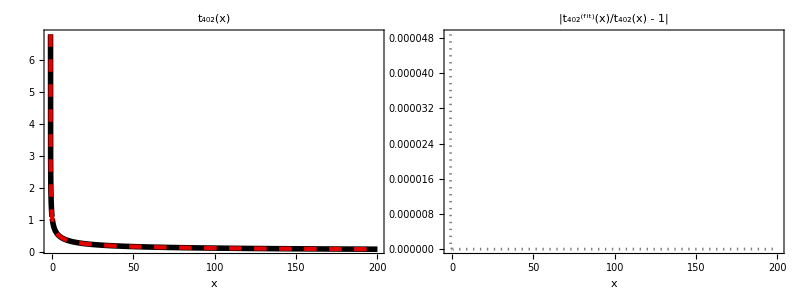

(-782.6241458110353 + 2877.4937140681823*x + 11666.945973644832*Power(x,2) + 8209.405189330819*Power(x,3) - 1491.7416191099312*Power(x,4) + 2351.8535113214166*Power(x,5) + 
     4676.460585239748*Power(x,6) + 233.1658473312586*Power(x,7) + 3847.444607895792*Power(x,8) + 8218.087686921586*Power(x,9) + 5185.441182809942*Power(x,10) + 
     1350.9463388535519*Power(x,11) + 144.6813790307555*Power(x,12) + 5.730779869275215*Power(x,13) + 0.07199605279826411*Power(x,14) + 0.0002191395134614306*Power(x,15) + 
     7.00328863503514e-8*Power(x,16))/
   (-733.7101279175023 + 2383.202992648816*x + 12168.766064060474*Power(x,2) + 12071.780843634386*Power(x,3) + 942.438393895715*Power(x,4) + 1269.190777932744*Power(x,5) + 
     5587.3197958329*Power(x,6) + 1747.4662503295506*Power(x,7) + 3439.1378626879673*Power(x,8) + 9328.567205945315*Power(x,9) + 7754.063179602607*Power(x,10) + 
     2770.050106683396*Power(x,11) + 439.9397079946307*Power(x,12) + 28.332872673857835*Power(x,13) + 0.639908201951777*Power(x,14) + 0.004139070893590553*Power(x,15) + 
     4.968575689502532e-6*Power(x,16))

```mathematica
δ=0.004;

t402[x_] = Piecewise[{{(3.0*(x-1.0)+(3.0+(x*(3.0*x-2.0)))*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x*x),x>δ},{1.0666666666666667-0.45714285714285713 x+0.3047619047619048 x^2-0.23088023088023085 x^3+0.1864801864801865 x^4-0.15664335664335666 x^5+0.13514328808446457 x^6-0.11888544891640866 x^7+0.10614772224679345 x^8-0.09589190367222403 x^9+0.08745341614906832 x^10,-δ≤x≤δ},{(3.0*(x-1.0)+(3.0+(x*(3.0*x-2.0)))*ArcTanh[Sqrt[-x]]/Sqrt[-x])/(4.0*x*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.01;
tdata=Table[{x,t402[x]},{x,xmin,xmax,xstep}];

n = 16;

t402fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t402[x],t402fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_402(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t402fit[x]/t402[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_402^(fit)(x)/t_402(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t402fit[x]//CForm
```

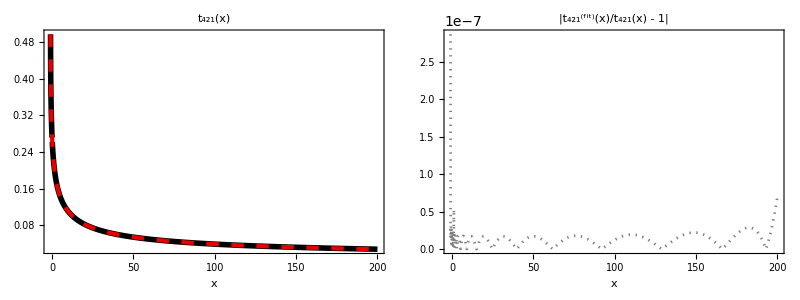

(-420.65125779019604 + 464.28029537808857*x + 3246.0671906277103*Power(x,2) + 2098.237776364318*Power(x,3) - 1061.9549124835105*Power(x,4) + 532.7983558552136*Power(x,5) + 
     914.6141784226661*Power(x,6) - 2418.6530038230967*Power(x,7) - 2652.892648012059*Power(x,8) - 416.8478662195916*Power(x,9) + 363.4944854153988*Power(x,10) + 
     145.17547168536962*Power(x,11) + 16.972162791609925*Power(x,12) + 0.6693300232722256*Power(x,13) + 0.008148267235988629*Power(x,14) + 
     0.000023934980557864453*Power(x,15) + 7.4068454059322425e-9*Power(x,16))/
   (-1577.442188404056 + 1290.35348266619*x + 12766.771913831271*Power(x,2) + 11195.127927858319*Power(x,3) - 2403.8898621960525*Power(x,4) + 675.83675733029*Power(x,5) + 
     4295.662325468036*Power(x,6) - 8343.96307877952*Power(x,7) - 12618.627251409462*Power(x,8) - 3834.7232116058217*Power(x,9) + 1267.6644115040936*Power(x,10) + 
     897.4182513912277*Power(x,11) + 159.92103119712186*Power(x,12) + 10.237581260406852*Power(x,13) + 0.22263552961633887*Power(x,14) + 0.001382377475563293*Power(x,15) + 
     1.6010885095334335e-6*Power(x,16))

```mathematica
δ=0.004;

t421[x_] = Piecewise[{{(3.0+x+(x+1.0)*(x-3.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x*x),x>δ},{0.2666666666666666-0.0761904761904762 x+0.0380952380952381 x^2-0.023088023088023088 x^3+0.015540015540015537 x^4-0.011188811188811189 x^5+0.00844645550527904 x^6-0.006604747162022705 x^7+0.005307386112339673 x^8-0.004358722894192001 x^9+0.0036438923395445133 x^10,-δ≤x≤δ},{(3.0+x+(x+1.0)*(x-3.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/(4.0*x*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t421[x]},{x,xmin,xmax,xstep}];

n = 16;

t421fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t421[x],t421fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_421(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t421fit[x]/t421[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_421^(fit)(x)/t_421(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t421fit[x]//CForm
```

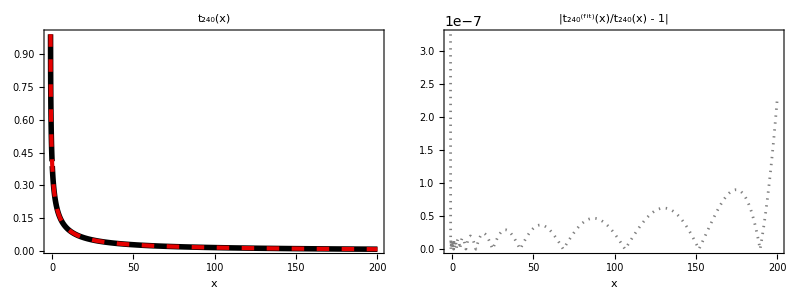

(1.3720294166387537 + 6.479852000152795*x + 10.674169713652642*Power(x,2) + 5.169007363561801*Power(x,3) - 3.2116648967117287*Power(x,4) - 0.22475691367143477*Power(x,5) + 
     8.686762977404275*Power(x,6) + 10.005974476850275*Power(x,7) + 5.034803866987541*Power(x,8) + 1.2717868202602456*Power(x,9) + 0.15316918932254478*Power(x,10) + 
     0.007525375309496188*Power(x,11) + 0.00011918947318522904*Power(x,12) + 4.0894729732006994e-7*Power(x,13) + 7.0252156834870885e-12*Power(x,14))/
   (3.4300735376520386 + 17.669661801447848*x + 33.441453744166616*Power(x,2) + 23.56721558534057*Power(x,3) - 3.573763832437269*Power(x,4) - 
     4.227477980097273*Power(x,5) + 21.976425366171526*Power(x,6) + 34.11871957610773*Power(x,7) + 22.248504845869782*Power(x,8) + 7.6982741500461715*Power(x,9) + 
     1.430767739136272*Power(x,10) + 0.1322275008597089*Power(x,11) + 0.005229441145770586*Power(x,12) + 0.00007049840241423675*Power(x,13) + 
     2.1570872744363772e-7*Power(x,14))

```mathematica
δ=0.004;

t240[x_] = Piecewise[{{(3.+2. x-3. (1.+x) ArcTan[√x]/√x)/(x*x),x>δ},{0.3999999999999999-0.17142857142857149 x+0.09523809523809523 x^2-0.06060606060606058 x^3+0.04195804195804195 x^4-0.030769230769230785 x^5+0.023529411764705882 x^6-0.01857585139318886 x^7+0.015037593984962405 x^8-0.0124223602484472 x^9+0.010434782608695646 x^10,-δ≤x≤δ},{(3.+2. x-3. (1.+x) ArcTanh[√-x]/√-x)/(x*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t240[x]},{x,xmin,xmax,xstep}];

n = 14;

t240fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t240[x],t240fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_240(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t240fit[x]/t240[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_240^(fit)(x)/t_240(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t240fit[x]//CForm
```

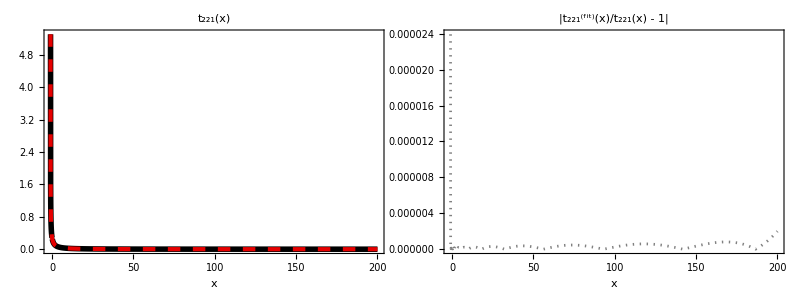

(0.23639553564018087 + 0.6188388060432732*x + 0.3912951752898536*Power(x,2) - 0.01271259655736948*Power(x,3) + 0.19394933153546515*Power(x,4) + 
     0.281111646843348*Power(x,5) + 0.16204423512073926*Power(x,6) + 0.3405714237429378*Power(x,7) + 0.37287213840322525*Power(x,8) + 0.14456213155467507*Power(x,9) + 
     0.016311508588690474*Power(x,10) + 0.0004999413708625376*Power(x,11) + 3.4661612010445846e-6*Power(x,12) + 2.853459851379285e-9*Power(x,13) - 
     5.999176868656615e-13*Power(x,14))/
   (0.8864833607982586 + 3.08048915472817*x + 3.474571877822368*Power(x,2) + 1.267433253553823*Power(x,3) + 0.7338705509446972*Power(x,4) + 1.677242381824388*Power(x,5) + 
     1.5236694094368166*Power(x,6) + 1.8296353995063672*Power(x,7) + 2.5085904119181768*Power(x,8) + 1.7699789074069745*Power(x,9) + 0.5656514996606236*Power(x,10) + 
     0.07110557742021892*Power(x,11) + 0.0030859751117327046*Power(x,12) + 0.00003850185162612134*Power(x,13) + 9.546131574190954e-8*Power(x,14))

```mathematica
δ=0.004;

t221[x_] = Piecewise[{{(-3.+(3.+x) ArcTan[√x]/√x)/(x*x),x>δ},{0.2666666666666668-0.22857142857142854 x+0.19047619047619047 x^2-0.1616161616161616 x^3+0.13986013986013987 x^4-0.12307692307692308 x^5+0.10980392156862744 x^6-0.09907120743034055 x^7+0.09022556390977443 x^8-0.08281573498964803 x^9+0.07652173913043478 x^10,-δ≤x≤δ},{(-3.+(3.+x) ArcTanh[√-x]/√-x)/(x*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t221[x]},{x,xmin,xmax,xstep}];

n = 14;

t221fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};
Grid[{{Plot[{t221[x],t221fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_221(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t221fit[x]/t221[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_221^(fit)(x)/t_221(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t221fit[x]//CForm
```

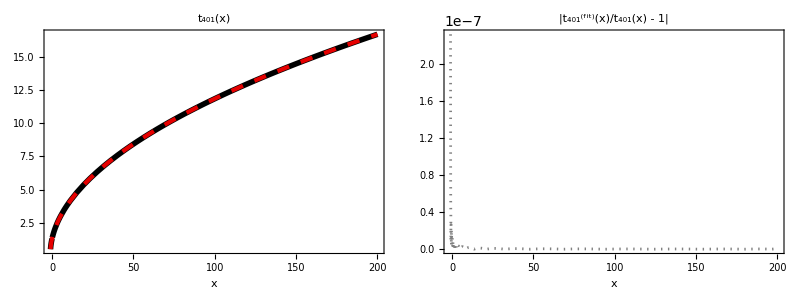

(9.623170814705219 + 53.473565015597735*x + 113.45883540125175*Power(x,2) + 94.9516120272897*Power(x,3) - 29.72287884877731*Power(x,4) - 130.9612218199621*Power(x,5) - 
     111.28354570856582*Power(x,6) - 36.20768632228901*Power(x,7) + 4.75756204373995*Power(x,8) + 7.7882996538990605*Power(x,9) + 2.5735263975249443*Power(x,10) + 
     0.388650327203954*Power(x,11) + 0.027365277763754404*Power(x,12) + 0.000826143389339139*Power(x,13) + 9.457243252497771e-6*Power(x,14) + 
     3.390895206924229e-8*Power(x,15) + 2.46207195777402e-11*Power(x,16))/
   (7.217378017444146 + 37.21822204050766*x + 70.82547074620173*Power(x,2) + 45.79871232996831*Power(x,3) - 35.802501745350256*Power(x,4) - 81.96779153107636*Power(x,5) - 
     54.40591073527847*Power(x,6) - 10.742421967501517*Power(x,7) + 5.373047447254023*Power(x,8) + 3.6814639397351057*Power(x,9) + 0.8700721697944566*Power(x,10) + 
     0.0937477802202806*Power(x,11) + 0.004460801632034925*Power(x,12) + 0.00008512168505937911*Power(x,13) + 5.648573633323026e-7*Power(x,14) + 
     9.956656265225061e-10*Power(x,15) + 2.0035798495377888e-13*Power(x,16))

```mathematica
δ=0.004;

t401[x_] = Piecewise[{{(1.0+3.0*x+(3.0*x-1.0)*(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x),x>δ},{1.3333333333333335+0.5333333333333333 x-0.11428571428571427 x^2+0.05079365079365082 x^3-0.02886002886002885 x^4+0.01864801864801864 x^5-0.01305361305361305 x^6+0.00965309200603319 x^7-0.007430340557275546 x^8+0.005897095680377412 x^9-0.004794595183611201 x^10,-δ≤x≤δ},{(1.0+3.0*x+(3.0*x-1.0)*(x+1.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/(4.0*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t401[x]},{x,xmin,xmax,xstep}];

n = 12;

t401fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};

Grid[{{Plot[{t401[x],t401fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_401(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t401fit[x]/t401[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_401^(fit)(x)/t_401(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t401fit[x]//CForm
```

```mathematica
Series[(x-1.0+(x+1.0)*(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x),{x,0,10}]
```

0.666667+0.133333 x-0.0190476 x^2+0.00634921 x^3-0.002886 x^4+0.001554 x^5-0.000932401 x^6+0.000603318 x^7-0.000412797 x^8+0.000294855 x^9-0.000217936 x^10+O[x]^(21/2)

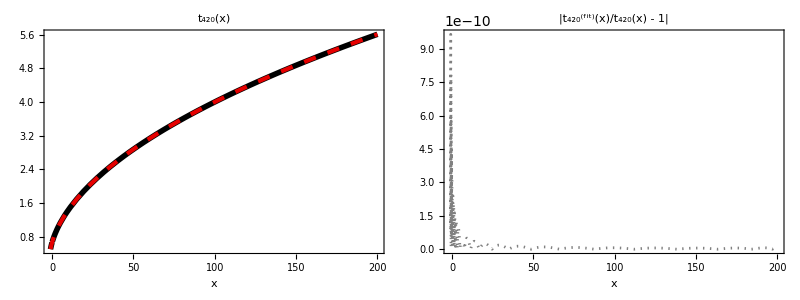

(47.4703542295881 + 177.19534084081312*x + 246.6926792681631*Power(x,2) + 155.98271035210664*Power(x,3) + 64.969162072131*Power(x,4) + 70.88941508098752*Power(x,5) + 
     77.68743157451306*Power(x,6) + 43.91816005728044*Power(x,7) + 13.077929698924496*Power(x,8) + 2.0746498517325604*Power(x,9) + 0.16973947393818437*Power(x,10) + 
     0.006743522002031799*Power(x,11) + 0.00012020682137512256*Power(x,12) + 8.62330447348284e-7*Power(x,13) + 2.0655895136779513e-9*Power(x,14) + 
     1.063930248968434e-12*Power(x,15))/
   (71.20553132170774 + 251.55190497160106*x + 321.7630824066435*Power(x,2) + 176.1304997115676*Power(x,3) + 69.33338748507218*Power(x,4) + 95.3583188305929*Power(x,5) + 
     98.66914436141671*Power(x,6) + 48.50744274189405*Power(x,7) + 11.982385620077034*Power(x,8) + 1.492323558296594*Power(x,9) + 0.09021603792342349*Power(x,10) + 
     0.0024944440890859857*Power(x,11) + 0.000029067778620099315*Power(x,12) + 1.251484429924204e-7*Power(x,13) + 1.5214909564945795e-10*Power(x,14) + 
     2.232209445225883e-14*Power(x,15))

```mathematica
δ=0.004;

t420[x_] = Piecewise[{{(x-1.0+(x+1.0)*(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x),x>δ},{0.6666666666666667+0.13333333333333336 x-0.019047619047619035 x^2+0.006349206349206354 x^3-0.0028860028860028877 x^4+0.0015540015540015523 x^5-0.0009324009324009307 x^6+0.0006033182503770752 x^7-0.00041279669762641844 x^8+0.0002948547840188713 x^9-0.00021793614470960038 x^10,-δ≤x≤δ},{(x-1.0+(x+1.0)*(x+1.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/(4.0*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t420[x]},{x,xmin,xmax,xstep}];

n = 15;

t420fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};

Grid[{{Plot[{t420[x],t420fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_420(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t420fit[x]/t420[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_420^(fit)(x)/t_420(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t420fit[x]//CForm
```

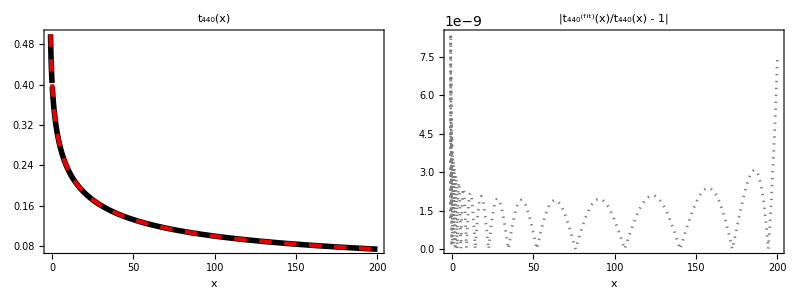

(47.4703542295881 + 177.19534084081312*x + 246.6926792681631*Power(x,2) + 155.98271035210664*Power(x,3) + 64.969162072131*Power(x,4) + 70.88941508098752*Power(x,5) + 
     77.68743157451306*Power(x,6) + 43.91816005728044*Power(x,7) + 13.077929698924496*Power(x,8) + 2.0746498517325604*Power(x,9) + 0.16973947393818437*Power(x,10) + 
     0.006743522002031799*Power(x,11) + 0.00012020682137512256*Power(x,12) + 8.62330447348284e-7*Power(x,13) + 2.0655895136779513e-9*Power(x,14) + 
     1.063930248968434e-12*Power(x,15))/
   (71.20553132170774 + 251.55190497160106*x + 321.7630824066435*Power(x,2) + 176.1304997115676*Power(x,3) + 69.33338748507218*Power(x,4) + 95.3583188305929*Power(x,5) + 
     98.66914436141671*Power(x,6) + 48.50744274189405*Power(x,7) + 11.982385620077034*Power(x,8) + 1.492323558296594*Power(x,9) + 0.09021603792342349*Power(x,10) + 
     0.0024944440890859857*Power(x,11) + 0.000029067778620099315*Power(x,12) + 1.251484429924204e-7*Power(x,13) + 1.5214909564945795e-10*Power(x,14) + 
     2.232209445225883e-14*Power(x,15))

```mathematica
δ=0.004;

t440[x_] = Piecewise[{{(-(3.0+5.0*x)+3.0*(x+1.0)*(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x*x),x>δ},{0.4000000000000001-0.057142857142857106 x+0.019047619047619063 x^2-0.008658008658008663 x^3+0.004662004662004657 x^4-0.002797202797202792 x^5+0.0018099547511312257 x^6-0.0012383900928792553 x^7+0.0008845643520566139 x^8-0.0006538084341288011 x^9+0.0004968944099378887 x^10,-δ≤x≤δ},{(-(3.0+5.0*x)+3.0*(x+1.0)*(x+1.0)*ArcTanh[Sqrt[-x]]/Sqrt[-x])/(4.0*x*x), -1.<x<-δ}}];

xmin = -0.999;
xmax = 200;
xstep=0.005;
tdata=Table[{x,t440[x]},{x,xmin,xmax,xstep}];

n = 14;

t440fit[x_]=rationalPolyFit[tdata,n,n]/.{x->x};

Grid[{{Plot[{t440[x],t440fit[x]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["t_440(x)",FontSize->24],FrameLabel->{"x",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[t440fit[x]/t440[x]-1.0]},{x,xmin,xmax},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|t_440^(fit)(x)/t_440(x) - 1|",FontSize->24],FrameLabel->{x,""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
t420fit[x]//CForm
```

```mathematica
Series[(-(3.0+5.0*x)+3.0*(x+1.0)*(x+1.0)*ArcTan[Sqrt[x]]/Sqrt[x])/(4.0*x*x),{x,0,10}]
```

0.4-0.0571429 x+0.0190476 x^2-0.00865801 x^3+0.004662 x^4-0.0027972 x^5+0.00180995 x^6-0.00123839 x^7+0.000884564 x^8-0.000653808 x^9+0.000496894 x^10+O[x]^(21/2)